## Annihilations

```mathematica
ClearSystemCache[]
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
tempConversion = (1*^-9/(1.16*^4)); (* GeV *)
NM     = (0.939); (* GeV *)
SOL   = 299792458.; (* ms^-1 *)
VELDISP  = 270.*^3;(* ms^-1 *)
NSVEL =  200.*^3 ;(* ms^-1 *)
G       =  6.67408*^-11; (*Grav Constant*)
TT = ((1*^10 * 3.154*^7)/(6.58*^-16)*1*^9); (* therm time *)
hBar = 1.054571800*^-34;
```

## Matrix Elements

```mathematica
(*================================================================================================================================================================*)

(* s = scalar, p = psedoscalar, v = vector, a = axialvector *)

ssME[q_, dmm_] := 16*NM^2*dmm^2;

psME[q_, dmm_] := 4*NM^2*q^2;

pspsME[q_, dmm_] := q^4;
```

## Coupling constants (neutrons)

```mathematica
responseFn[q_, q0_] := (NM^2*q0)/(Pi*q);
denomInt[ki_, ME_, dmm_] :=Module[
{q, q0, cos},
q = √(ki^2+kp^2- 2* ki*kp*cos);
q0 = 1/(2*dmm)*(ki^2- kp^2);
 Integrate[(ME[q, dmm]*q0)/(16*NM^2*dmm^2*(2*π)^2)*kp^2*responseFn[q, q0],{kp, 0, ki}, {cos, -1, 1}, Assumptions->{ki>kp, kp>0}]
];

gSqr[ME_, dmm_, temp_] := Module[(*coupling constant squared in Natural units*)
{k0, kn,T},
T = temp*tempConversion;
k0 = dmm/3;
kn = Sqrt[3*T*dmm];
-1/TT*Integrate[ki/(dmm*denomInt[ki, ME, dmm]), {ki, k0, kn}, Assumptions->{k0>kn, kn>0}]
];
```

## Interpolating Functions

#### Load in data

```mathematica
EoSHeaders = Import["eos_24_lowmass.dat"];
Dataset[EoSHeaders[[1,All]]] (*Print out headings so I know what I'm doing *)
EoSData =Drop[EoSHeaders, 1] ;(* Remove Headings *)
```

Dataset[<>]

Make Interpolating Functions

```mathematica
radius = EoSData[[All,1]];

rMin = radius[[1]];
rMax = 12.1;

muFn     = Interpolation[ EoSData[[All, {1,8}]] ]; (* Chemical potential in MeV *)

nb          = EoSData[[All,3]];
Yn          = EoSData[[All, 7]];
muList = EoSData[[All, 8]];

(*ndList = nb*Yn;
nd          = Interpolation[ Transpose[{radius,nb*Yn}]]; (* Neutron density in fm^-1*)*)

NSMass=   Interpolation[EoSData[[All, {1, 2}]]]; (* In units of M_⊙ *) 
(*================================================================================================================================================================*)
potentialInside[rad_?NumericQ] := Which[rad ≤10.^-6, 0, True, NIntegrate[(NSMass[r])/r^2, {r, rMin, rad}]*(G*2.*^30)/(1.*^3*SOL^2)];
pot = Interpolation[Table[potentialInside[x], {x, 0, rMax}]];
(*================================================================================================================================================================*)
```

## Masses and other things

```mathematica
lepMasses = {0.5109989461, 105.6583745, 1776.86, 0,0,0}*1.*^-3;(* {e, μ, τ,Subscript[ν, e], Subscript[ν, μ], Subscript[ν, τ]}*)
quarkMasses = {2.2*^-3, 4.7*^-3, 95*^-3, 1.257, 4.18, 173};(* {u, d, s, c, b, t}  *) 

vAvg[mx_, temp_] := (6*temp*tempConversion)/mx;

capRate = 1.*^22*6.58*^-16*1*^-9; (*test cap rate*)
```

## Number density

Assume constant density over region interested:

```mathematica
rTh[mx_, temp_] := 3.265*(temp/10^5)^(1/2)*(1/mx)^(1/2);
ndAn[rad_, mx_, temp_, n_] := Exp[(-rad^2*n)/rTh[mx, temp]^2];
ndAnFac[mx_?NumericQ, temp_?NumericQ] := NIntegrate[ndAn[x,mx, temp, 2. ]*x^2, {x, 0, rTh[mx, temp]}]/(4.*π*(NIntegrate[ndAn[x, mx, temp, 1.]*x^2, {x, 0, rTh[mx, temp]}])^2);
```

General density profile

```mathematica
ndFac[mx_?NumericQ, temp_?NumericQ] :=NIntegrate[Exp[(-2.*mx*potentialInside[rad])/temp]*rad^2, {rad, rMin, rMax}]/(4.*Pi*(NIntegrate[Exp[(-mx*potentialInside[rad])/temp]*rad^2, {rad, rMin, rMax}])^2);
```

Testing finding thermal radius

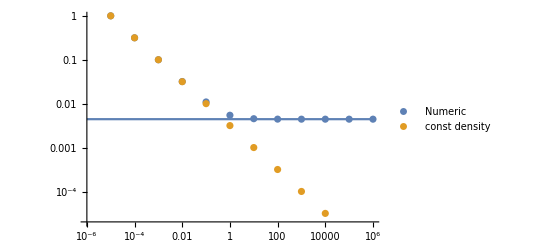

```mathematica
Show[LogLogPlot[rMin, {x, 1*^-6, 1*^6}],
ListLogLogPlot[{With[{m :=10.^mp},Table[{m, x/.FindRoot[m*potentialInside[x] == 3./2*8.62069*10^-9,{x, 0.001}]}, {mp, -6, 6,1}]], With[{m :=10.^mp},Table[{m, rTh[m,10^5]/1*^3
}, {mp, -6, 6,1}]]}, AxesLabel->{"m_χ [GeV]", "r_th [km]"}, PlotLegends->{"Numeric", "const density"}]]
```

## Thermally averaged annihilation cross sections

```mathematica
ssACS[mx_, temp_] :=(Sum[mx^2/(16.*π)*(1. - mf^2/mx^2)^(3/2)*vAvg[mx, temp], {mf, Select[lepMasses, #≤ mx&]}]+Sum[(3.*mx^2)/(16.*π)*(1. - mf^2/mx^2)^(3/2)*vAvg[mx, temp], {mf, Select[quarkMasses, #≤ mx&]}] );
(*================================================================================================================================================================*)

ppACS[mx_, temp_] :=(Sum[1./(4.*π)*mx^2*Sqrt[1. - mf^2/mx^2](**(1. + ((2.*mx^2- mf)/(8.*(mx^2 - mf^2)))*vAvg[mx, temp])*),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[3./(4.*π)*mx^2*Sqrt[1. - mf^2/mx^2](**(1. +( (2.*mx^2- mf)/(8.*(mx^2 - mf^2)))*vAvg[mx, temp])*),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

vvACS[mx_, temp_] := (Sum[1./(4.*π)*mx^2*Sqrt[1. - mf^2/mx^2]*((2. +mf^2/mx^2) + 1./12.*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[3./(4.*π)*mx^2 Sqrt[1. - mf^2/mx^2]*((2. +mf^2/mx^2) + 1./12.*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)


aaACS[mx_, temp_] := (Sum[1./(4.*π)*mx^2*Sqrt[1. - mf^2/mx^2]*(mf^2/mx^2 + 1./12.*(2. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[3./(4.*π)*mx^2*Sqrt[1. - mf^2/mx^2]*(mf^2/mx^2 + 1./12.*(2. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);

(*================================================================================================================================================================*)

ttACS[mx_, temp_] := (Sum[1./(4.*π)*mx^2*Sqrt[1. - mf^2/mx^2]*((7.+mf^2/mx^2) + 2./3.*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[lepMasses, #≤ mx&]}] +
Sum[3./(4.*π)*mx^2*Sqrt[1. - mf^2/mx^2]*((7.+mf^2/mx^2) + 2./3.*(1. - mf^2/mx^2)*vAvg[mx, temp]),{mf, Select[quarkMasses, #≤ mx&]}]);
```

## Equilibrium time

```mathematica
anG[ACS_, mx_?NumericQ, temp_?NumericQ] :=1./(0.5*TT*Sqrt[capRate*ndAnFac[mx, temp]*ACS[mx,temp]]);
```

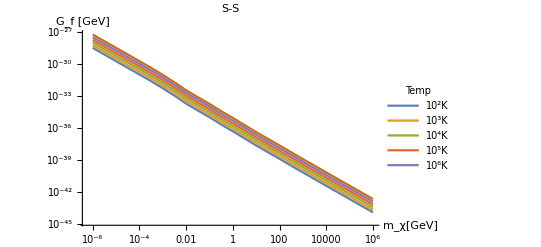

```mathematica
ListLogLogPlot[
 Evaluate@Table[
With[{x:=10^xp},
Table[{x,anG[ssACS, x, T]},{xp, -6, 6, 0.5}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}
],
PlotLegends->LineLegend[Table[T,{T, {"10^2K","10^3K","10^4K", "10^5K", "10^6K"}} ],LegendLabel->"Temp"], 
Joined->True, 
AxesLabel->{"m_χ[GeV]", "G_f [GeV]"}, 
PlotLabel->"S-S", 
LabelStyle->Directive[Black,Bold]]

(*High temp, low mass issue where does not thermalise*)
```

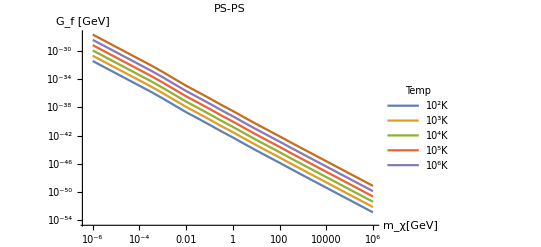

```mathematica
ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[ppACS, x, T]},{xp, -6, 6, 0.5}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}],PlotLegends->LineLegend[Table[T,{T, {"10^2K","10^3K","10^4K", "10^5K", "10^6K"}} ],LegendLabel->"Temp"], Joined->True,AxesLabel->{"m_χ[GeV]", "G_f [GeV]"}, PlotLabel->"PS-PS", LabelStyle->Directive[Black,Bold]]
```

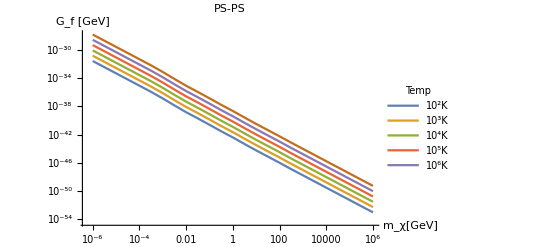

```mathematica
ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[vvACS, x, T]},{xp, -6, 6, 0.5}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}],PlotLegends->LineLegend[Table[T,{T, {"10^2K","10^3K","10^4K", "10^5K", "10^6K"}} ],LegendLabel->"Temp"], Joined->True,AxesLabel->{"m_χ[GeV]", "G_f [GeV]"}, PlotLabel->"PS-PS", LabelStyle->Directive[Black,Bold]]
```

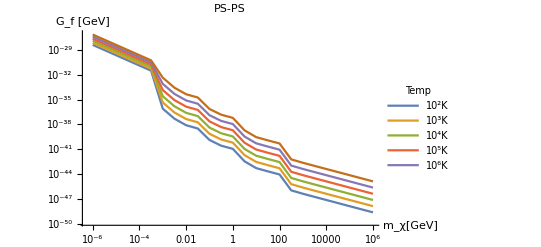

```mathematica
ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[aaACS, x, T]},{xp, -6, 6, 0.5}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}],PlotLegends->LineLegend[Table[T,{T, {"10^2K","10^3K","10^4K", "10^5K", "10^6K"}} ],LegendLabel->"Temp"], Joined->True,AxesLabel->{"m_χ[GeV]", "G_f [GeV]"}, PlotLabel->"PS-PS", LabelStyle->Directive[Black,Bold]]
```

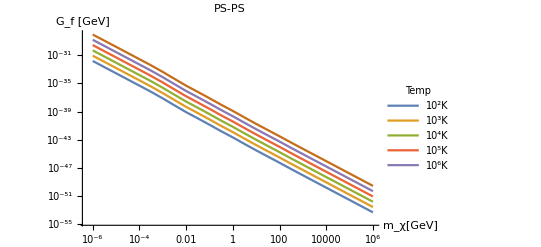

```mathematica
ListLogLogPlot[ Evaluate@Table[With[{x:=10^xp},Table[{x,anG[ttACS, x, T]},{xp, -6, 6, 0.5}]] ,{T, {10.^1,10.^2,10.^3, 10.^4, 10.^5, 10.^6}}],PlotLegends->LineLegend[Table[T,{T, {"10^2K","10^3K","10^4K", "10^5K", "10^6K"}} ],LegendLabel->"Temp"], Joined->True,AxesLabel->{"m_χ[GeV]", "G_f [GeV]"}, PlotLabel->"PS-PS", LabelStyle->Directive[Black,Bold]]
```